```mathematica
(* This notebook aggregates the formulae Catani uses in his 1991 paper to resum the thrust rate *)
```

```mathematica
ClearGlobal[];
RemoveGlobal[];
```

```mathematica
Cf=4/3
Nf=5
```

4/3

5

```mathematica
C1=(Cf/(2Pi))*(-5/2+Pi^2/3)
C2=0
C3=0
```

(2 (-5/2+π^2/3))/(3 π)

0

0

```mathematica
A1=Cf
A2=(Cf/2)*(67/6-Pi^2/2-5 Nf/9)
B1=-3 Cf/2
beta0=(33-2 Nf)/(12 Pi)
beta1=(153-19 Nf)/(24 Pi^2)
```

4/3

2/3 (151/18-π^2/2)

-2

23/(12 π)

29/(12 π^2)

```mathematica
scriptG[lnx_,α_,ratsqr_]=(-A1/(Pi beta0))*((1-2 beta0 α lnx)Log[1-2 beta0 α lnx]/(beta0 α)-2(1-beta0 α lnx)Log[1- beta0 α lnx]/(beta0 α))+(A1 Pi beta0 Log[ratsqr]-A2)(2 Log[1-beta0 α lnx]-Log[1-2 beta0 α lnx])/(beta0^2Pi^2)+B1 Log[1-beta0 α lnx ]/(Pi beta0)-2 A1 EulerGamma (Log[1- beta0 α lnx]-Log[1-2 beta0 α lnx])/(Pi beta0) - A1 beta1 (Log[1-2 beta0 α lnx]-2Log[1-beta0 α lnx])/(Pi beta0^3)+Power[Log[1-2 beta0 α lnx],2]/2 -Power[Log[1-beta0 α lnx],2]
```

1/2 Log[1-(23 lnx α)/(6 π)]^2-(5568 (Log[1-(23 lnx α)/(6 π)]-2 Log[1-(23 lnx α)/(12 π)]))/12167-24/23 Log[1-(23 lnx α)/(12 π)]-Log[1-(23 lnx α)/(12 π)]^2-32/23 EulerGamma (-Log[1-(23 lnx α)/(6 π)]+Log[1-(23 lnx α)/(12 π)])+144/529 (-2/3 (151/18-π^2/2)+(23 Log[ratsqr])/9) (-Log[1-(23 lnx α)/(6 π)]+2 Log[1-(23 lnx α)/(12 π)])-16/23 ((12 π (1-(23 lnx α)/(6 π)) Log[1-(23 lnx α)/(6 π)])/(23 α)-(24 π (1-(23 lnx α)/(12 π)) Log[1-(23 lnx α)/(12 π)])/(23 α))

```mathematica
scriptT[lnx_,α_]=1+2 A1 (Log[1+beta0 α lnx]-Log[1+2 beta0 α lnx])/(Pi beta0)
```

1+32/23 (Log[1+(23 lnx α)/(12 π)]-Log[1+(23 lnx α)/(6 π)])

```mathematica
Σ[τ_,α_,ratsqr_]=Exp[scriptG[-Log[τ],α,ratsqr]]/Gamma[scriptT[Log[τ],α]]
```

ⅇ^(-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+144/529 (-2/3 (151/18-π^2/2)+(23 Log[ratsqr])/9) (2 Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2-(5568 (-2 Log[1+(23 α Log[τ])/(12 π)]+Log[1+(23 α Log[τ])/(6 π)]))/12167-16/23 (-(24 π (1+(23 α Log[τ])/(12 π)) Log[1+(23 α Log[τ])/(12 π)])/(23 α)+(12 π (1+(23 α Log[τ])/(6 π)) Log[1+(23 α Log[τ])/(6 π)])/(23 α)))/(Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (1+(23 α Log[τ])/(12 π))^(24/23))

```mathematica
Cc[α_]=1+C1*α+C2*α^2+C3*α^3
```

1+(2 (-5/2+π^2/3) α)/(3 π)

```mathematica
F[τ_,α_]=α*(Cf/(2Pi))*(6τ(1+Log[τ])+4Log[τ]Log[1-τ]-2Power[Log[1-τ],2]+3(1-2τ)Log[1-2τ]+9τ^2/2-4PolyLog[2,τ/(1-τ)])
```

1/(3 π)2 α ((9 τ^2)/2+3 (1-2 τ) Log[1-2 τ]-2 Log[1-τ]^2+4 Log[1-τ] Log[τ]+6 τ (1+Log[τ])-4 PolyLog[2,τ/(1-τ)])

```mathematica
rateR[τ_,α_,ratsqr_]=Cc[α]*Σ[τ,α,ratsqr]+F[τ,α] // Simplify
```

2/3 ((ⅇ^(-(16 (-151+9 π^2+69 Log[ratsqr]) (Log[24 π]+Log[6 π+23 α Log[τ]]-2 Log[12 π+23 α Log[τ]]))/1587-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2) (9 π-15 α+2 π^2 α) (1+(23 α Log[τ])/(12 π))^(32/529 ((12 π)/α+23 Log[τ])) (1+(23 α Log[τ])/(6 π))^(-(32 (6 π+23 α Log[τ]))/(529 α)))/(2^(3479/12167) (3 π)^(5039/12167) Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (6 π+23 α Log[τ])^(5568/12167) (12 π+23 α Log[τ])^(1560/12167))+1/π α (6 τ+(9 τ^2)/2+(3-6 τ) Log[1-2 τ]-2 Log[1-τ]^2+6 τ Log[τ]+4 Log[1-τ] Log[τ]-4 PolyLog[2,τ/(1-τ)]))

```mathematica
rateRta[τ_,α_]=rateR[τ,α,1]
```

2/3 ((ⅇ^(-(16 (-151+9 π^2) (Log[24 π]+Log[6 π+23 α Log[τ]]-2 Log[12 π+23 α Log[τ]]))/1587-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2) (9 π-15 α+2 π^2 α) (1+(23 α Log[τ])/(12 π))^(32/529 ((12 π)/α+23 Log[τ])) (1+(23 α Log[τ])/(6 π))^(-(32 (6 π+23 α Log[τ]))/(529 α)))/(2^(3479/12167) (3 π)^(5039/12167) Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (6 π+23 α Log[τ])^(5568/12167) (12 π+23 α Log[τ])^(1560/12167))+1/π α (6 τ+(9 τ^2)/2+(3-6 τ) Log[1-2 τ]-2 Log[1-τ]^2+6 τ Log[τ]+4 Log[1-τ] Log[τ]-4 PolyLog[2,τ/(1-τ)]))

```mathematica
diffrateRta[τ_,α_]=D[rateRta[τ,α],τ]
```

2/3 (-((260 2^(8688/12167) 3^(7128/12167) ⅇ^(-(16 (-151+9 π^2) (Log[24 π]+Log[6 π+23 α Log[τ]]-2 Log[12 π+23 α Log[τ]]))/1587-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2) α (9 π-15 α+2 π^2 α) (1+(23 α Log[τ])/(12 π))^(32/529 ((12 π)/α+23 Log[τ])) (1+(23 α Log[τ])/(6 π))^(-(32 (6 π+23 α Log[τ]))/(529 α)))/(529 π^(5039/12167) τ Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (6 π+23 α Log[τ])^(5568/12167) (12 π+23 α Log[τ])^(13727/12167)))-(928 2^(8688/12167) 3^(7128/12167) ⅇ^(-(16 (-151+9 π^2) (Log[24 π]+Log[6 π+23 α Log[τ]]-2 Log[12 π+23 α Log[τ]]))/1587-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2) α (9 π-15 α+2 π^2 α) (1+(23 α Log[τ])/(12 π))^(32/529 ((12 π)/α+23 Log[τ])) (1+(23 α Log[τ])/(6 π))^(-(32 (6 π+23 α Log[τ]))/(529 α)))/(529 π^(5039/12167) τ Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (6 π+23 α Log[τ])^(17735/12167) (12 π+23 α Log[τ])^(1560/12167))+1/π α (12-(2 (3-6 τ))/(1-2 τ)+9 τ-6 Log[1-2 τ]+(4 Log[1-τ])/(1-τ)+(4 Log[1-τ])/τ+6 Log[τ]-(4 Log[τ])/(1-τ)+(4 (1-τ) (1/(1-τ)+τ/(1-τ)^2) Log[1-τ/(1-τ)])/τ)+(ⅇ^(-(16 (-151+9 π^2) (Log[24 π]+Log[6 π+23 α Log[τ]]-2 Log[12 π+23 α Log[τ]]))/1587-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2) (9 π-15 α+2 π^2 α) (1+(23 α Log[τ])/(12 π))^(32/529 ((12 π)/α+23 Log[τ])) (1+(23 α Log[τ])/(6 π))^(-(32 (6 π+23 α Log[τ]))/(529 α)) ((8 α ((12 π)/α+23 Log[τ]))/(69 π τ (1+(23 α Log[τ])/(12 π)))+(32 Log[1+(23 α Log[τ])/(12 π)])/(23 τ)))/(2^(3479/12167) (3 π)^(5039/12167) Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (6 π+23 α Log[τ])^(5568/12167) (12 π+23 α Log[τ])^(1560/12167))+(ⅇ^(-(16 (-151+9 π^2) (Log[24 π]+Log[6 π+23 α Log[τ]]-2 Log[12 π+23 α Log[τ]]))/1587-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2) (9 π-15 α+2 π^2 α) (1+(23 α Log[τ])/(12 π))^(32/529 ((12 π)/α+23 Log[τ])) (1+(23 α Log[τ])/(6 π))^(-(32 (6 π+23 α Log[τ]))/(529 α)) (-(16 (6 π+23 α Log[τ]))/(69 π τ (1+(23 α Log[τ])/(6 π)))-(32 Log[1+(23 α Log[τ])/(6 π)])/(23 τ)))/(2^(3479/12167) (3 π)^(5039/12167) Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (6 π+23 α Log[τ])^(5568/12167) (12 π+23 α Log[τ])^(1560/12167))+(ⅇ^(-(16 (-151+9 π^2) (Log[24 π]+Log[6 π+23 α Log[τ]]-2 Log[12 π+23 α Log[τ]]))/1587-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2) (9 π-15 α+2 π^2 α) (1+(23 α Log[τ])/(12 π))^(32/529 ((12 π)/α+23 Log[τ])) (1+(23 α Log[τ])/(6 π))^(-(32 (6 π+23 α Log[τ]))/(529 α)) (-(16 (-151+9 π^2) ((23 α)/(τ (6 π+23 α Log[τ]))-(46 α)/(τ (12 π+23 α Log[τ]))))/1587-32/23 EulerGamma ((23 α)/(12 π τ (1+(23 α Log[τ])/(12 π)))-(23 α)/(6 π τ (1+(23 α Log[τ])/(6 π))))-(23 α Log[1+(23 α Log[τ])/(12 π)])/(6 π τ (1+(23 α Log[τ])/(12 π)))+(23 α Log[1+(23 α Log[τ])/(6 π)])/(6 π τ (1+(23 α Log[τ])/(6 π)))))/(2^(3479/12167) (3 π)^(5039/12167) Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (6 π+23 α Log[τ])^(5568/12167) (12 π+23 α Log[τ])^(1560/12167))-(16 2^(8688/12167) ⅇ^(-(16 (-151+9 π^2) (Log[24 π]+Log[6 π+23 α Log[τ]]-2 Log[12 π+23 α Log[τ]]))/1587-Log[1+(23 α Log[τ])/(12 π)]^2-32/23 EulerGamma (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])+1/2 Log[1+(23 α Log[τ])/(6 π)]^2) (9 π-15 α+2 π^2 α) (1+(23 α Log[τ])/(12 π))^(32/529 ((12 π)/α+23 Log[τ])) (1+(23 α Log[τ])/(6 π))^(-(32 (6 π+23 α Log[τ]))/(529 α)) ((23 α)/(12 π τ (1+(23 α Log[τ])/(12 π)))-(23 α)/(6 π τ (1+(23 α Log[τ])/(6 π)))) PolyGamma[0,1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])])/(23 (3 π)^(5039/12167) Gamma[1+32/23 (Log[1+(23 α Log[τ])/(12 π)]-Log[1+(23 α Log[τ])/(6 π)])] (6 π+23 α Log[τ])^(5568/12167) (12 π+23 α Log[τ])^(1560/12167)))

```mathematica
rateRta[0.499,0.116]
```

0.959438

```mathematica
sigmaLogseries1[τ_,α_]=Series[Log[Σ[τ,α,rat]],{α,0,4}]
sigmaLogseries2[τ_,α_]=Series[sigmaLogseries1[τ,α],{τ,0,4}]
```

-(2 (3 Log[τ]+2 Log[τ]^2) α)/(3 π)+((16681 Log[τ]^2-2576 π^2 Log[τ]^2+25392 Log[rat] Log[τ]^2+25392 Log[τ]^3) α^2)/(9936 π^2)+1/(5184 π^3)(-44471 Log[τ]^3+11040 π^2 Log[τ]^3-50784 Log[rat] Log[τ]^3-29624 Log[τ]^4+16384 Log[τ]^3 PolyGamma[2,1]) α^3+1/(3732480 π^4)(148643595 Log[τ]^4-40204000 π^2 Log[τ]^4-524288 π^4 Log[τ]^4+122643360 Log[rat] Log[τ]^4+52561440 Log[τ]^5-101744640 Log[τ]^4 PolyGamma[2,1]) α^4+O[α]^5

((-(2 Log[τ])/π-(4 Log[τ]^2)/(3 π))+O[τ]^5) α+((-7/27 Log[τ]^2+(16681 Log[τ]^2)/(9936 π^2)+(23 Log[rat] Log[τ]^2)/(9 π^2)+(23 Log[τ]^3)/(9 π^2))+O[τ]^5) α^2+((-(44471 Log[τ]^3)/(5184 π^3)+(115 Log[τ]^3)/(54 π)-(529 Log[rat] Log[τ]^3)/(54 π^3)-(3703 Log[τ]^4)/(648 π^3)+(256 Log[τ]^3 PolyGamma[2,1])/(81 π^3))+O[τ]^5) α^3+((-(512 Log[τ]^4)/3645+(3303191 Log[τ]^4)/(82944 π^4)-(251275 Log[τ]^4)/(23328 π^2)+(85169 Log[rat] Log[τ]^4)/(2592 π^4)+(12167 Log[τ]^5)/(864 π^4)-(736 Log[τ]^4 PolyGamma[2,1])/(27 π^4))+O[τ]^5) α^4+O[α]^5

```mathematica
tauseries[τ_,α_]=Series[rateRta[τ,α],{α,0,1}]
alphaseries[τ_,α_]=Series[tauseries[τ,α],{τ,0,1}] // FullSimplify
```

1+1/(9 π)(-15+2 π^2+36 τ+27 τ^2+18 Log[1-2 τ]-36 τ Log[1-2 τ]-12 Log[1-τ]^2-18 Log[τ]+36 τ Log[τ]+24 Log[1-τ] Log[τ]-12 Log[τ]^2-24 PolyLog[2,τ/(1-τ)]) α+O[α]^2

1+((-15+2 π^2-6 Log[τ] (3+2 Log[τ]))/(9 π)+(4 (-2+Log[τ]) τ)/(3 π)+O[τ]^2) α+O[α]^2

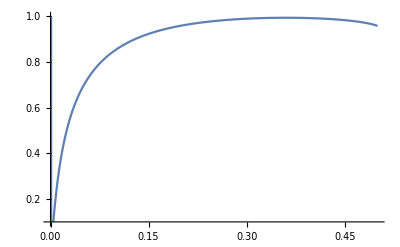

```mathematica
Plot[rateRta[τ,0.116],{τ,0,0.5},PlotRange->{0.1,1}]
```

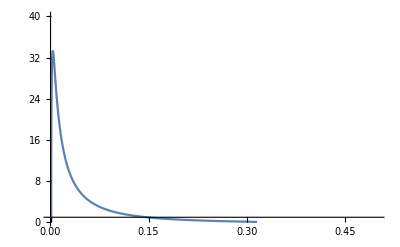

```mathematica
Plot[diffrateRta[τ,0.116],{τ,0,0.5},PlotRange->{0.1,40}]
```

```mathematica
alpha=0.118
alphabar=0.118*Cf/(2 Pi)
```

0.118

0.0250404

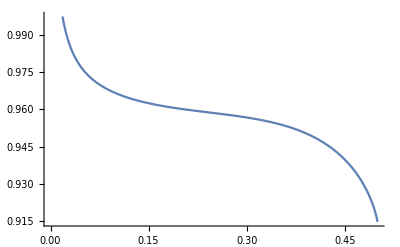

```mathematica
Plot[Cc[alpha]*Exp[alphabar*Log[x]+5.75*(alphabar*Log[x])^2-(64Zeta[3]/3)*(alphabar*Log[x])^3]+F[x,alpha],{x,0,0.5}]
```

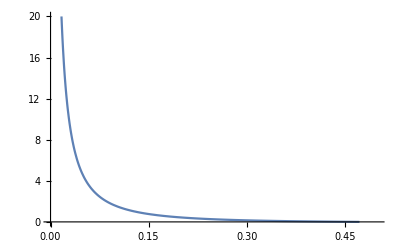

```mathematica
Plot[alphabar(-4Log[x]/x-3/x),{x,0,0.5},PlotRange->{0,20}]
```

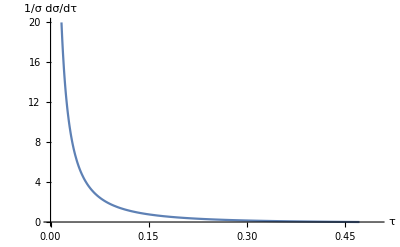

```mathematica
Show[%49,AxesLabel->{HoldForm[τ],HoldForm[1/σ]HoldForm[dσ/dτ]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

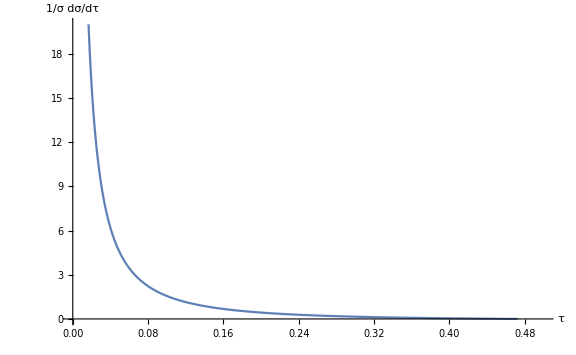

```mathematica
Show[%57,ImageSize->Large]
```

```mathematica
Export["/Users/Matt/Documents/Research/PhD Quals/my_fixedorder.png",%59,"PNG"]
```

/Users/Matt/Documents/Research/PhD Quals/my_fixedorder.png

```mathematica
Export["/Users/Matt/Documents/Research/PhD Quals/my_fixedorder.jpg",%57,"JPEG"]
```

/Users/Matt/Documents/Research/PhD Quals/my_fixedorder.jpg

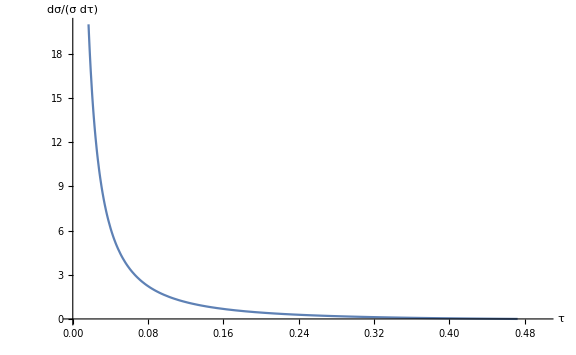

```mathematica
Show[%54,ImageSize->Large]
```